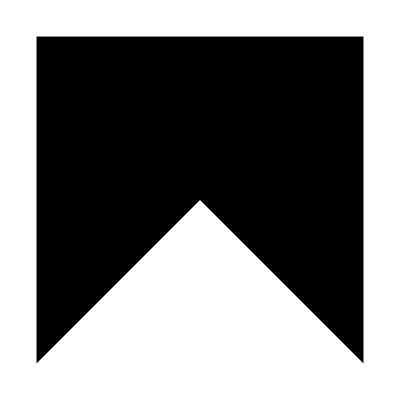

```mathematica
Graphics[Polygon@{{-0.5,0.},{0.,0.5},{0.5,0.},{0.5,1.},{-0.5,1.}}]
```

```mathematica
?DiscretizeGraphics
```

RowBox[{"DiscretizeGraphics", "[", StyleBox["g", "TI"], "]"}] discretizes a 2D or 3D graphic StyleBox["g", "TI"] into a MeshRegion.
RowBox[{"DiscretizeGraphics", "[", RowBox[{StyleBox["g", "TI"], ",", StyleBox["patt", "TI"]}], "]"}] discretizes only the elements in StyleBox["g", "TI"] that match the pattern StyleBox["patt", "TI"].

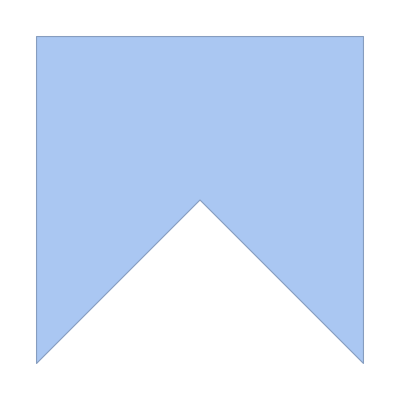

```mathematica
DiscretizeGraphics[Graphics[Polygon@{{-0.5,0.},{0.,0.5},{0.5,0.},{0.5,1.},{-0.5,1.}}]]
```

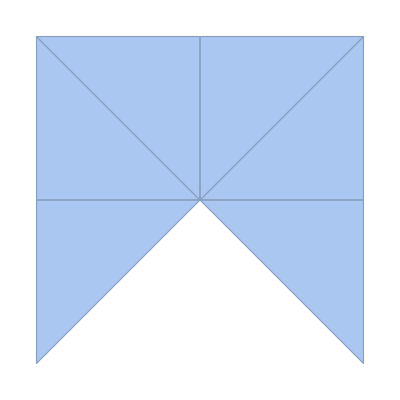

```mathematica
TriangulateMesh[DiscretizeGraphics[Graphics[Polygon@{{-0.5,0.},{0.,0.5},{0.5,0.},{0.5,1.},{-0.5,1.}}]],MaxCellMeasure->0.2]
```

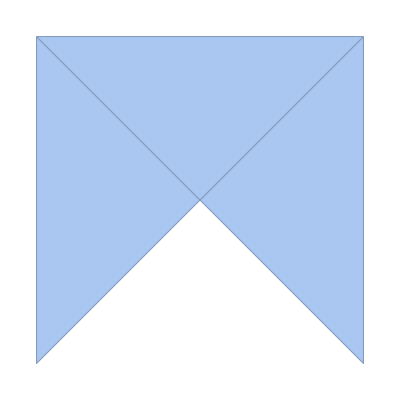

```mathematica
TriangulateMesh[DiscretizeGraphics[Graphics[Polygon@{{-0.5,0.},{0.,0.5},{0.5,0.},{0.5,1.},{-0.5,1.}}]],MaxCellMeasure->1]
```

```mathematica
meshregions=TriangulateMesh[DiscretizeGraphics[Graphics[Polygon@{{-0.5,0.},{0.,0.5},{0.5,0.},{0.5,1.},{-0.5,1.}}]],MaxCellMeasure->Infinity]
```

-Graphics-

```mathematica
MeshPrimitives[meshregions,2]
MeshPrimitives[meshregions,1]
```

{Polygon[{{-0.5,1.},{-0.5,0.},{0.,0.5}}],Polygon[{{0.,0.5},{0.5,0.},{0.5,1.}}],Polygon[{{0.,0.5},{0.5,1.},{-0.5,1.}}]}

{Line[{{-0.5,1.},{-0.5,0.}}],Line[{{-0.5,0.},{0.,0.5}}],Line[{{0.,0.5},{-0.5,1.}}],Line[{{0.,0.5},{0.5,0.}}],Line[{{0.5,0.},{0.5,1.}}],Line[{{0.5,1.},{0.,0.5}}],Line[{{0.5,1.},{-0.5,1.}}]}